```mathematica
noL1iData=Import[FileNameJoin[{NotebookDirectory[],"ipc1_correct_result_analysis/ipc1_no_l1i.csv"}],"Dataset","HearderLInes"->1]
```

```mathematica
items=Normal[noL1iData[All,{6,7,8,12,13,14,15,16,17}]];
```

```mathematica
noL1iMatrix=Drop[Normal[noL1iData[All,Range[3,13]]],1];
```

```mathematica
allPCs=PrincipalComponents[noL1iMatrix];
```

```mathematica
Variance[allPCs]
```

{5.67083×10^12,1.77095×10^12,1.39743×10^12,6.64521×10^11,102.722,8.05902,5.35087,9.9857×10^-10,5.32608×10^-10,0.,0.}

```mathematica
chosenVar=Drop[Variance[allPCs],-4]
(*chosenVar=Variance[allPCs]*)
```

{5.67083×10^12,1.77095×10^12,1.39743×10^12,6.64521×10^11,102.722,8.05902,5.35087}

```mathematica
chosenPCs=Transpose[Drop[Transpose[allPCs],-4]]
(*chosenPCs=allPCs*);
MatrixForm[chosenPCs]
```

{{2.05624×10^6,1.38362×10^6,677771.,1.92128×10^6,0.0571068,0.359755,1.28282},{-251439.,1.83471×10^6,811475.,-381605.,-4.00987,-1.19933,0.400265},{1.48117×10^6,1.50765×10^6,228763.,-328936.,-4.8617,-4.35663,-0.26013},{1.00203×10^6,1.23391×10^6,963976.,1.74467×10^6,3.57652,6.01429,-1.24721},{-1.29177×10^6,1.76392×10^6,1.11947×10^6,-1.00922×10^6,-5.68127,-1.19898,-2.34155},{3.99912×10^6,859098.,-1.05023×10^6,119716.,-2.76109,0.0882671,-1.14511},{1.18723×10^6,894662.,730117.,2.35936×10^6,3.52392,-1.40422,1.4488},{931609.,862734.,799228.,556258.,7.97394,0.475125,-1.89381},{2.16128×10^6,1.358×10^6,-225241.,-480380.,-4.9581,-4.07638,0.655252},{-4.35104×10^6,2.33398×10^6,2.00254×10^6,-910699.,-8.26884,-3.40053,0.196898},{1.52108×10^6,810504.,121659.,192701.,-0.897691,6.03954,1.53798},{488336.,-359784.,1.31655×10^6,-448138.,25.6003,-1.50416,-0.0161878},{563013.,-583983.,1.42995×10^6,-680288.,31.4587,-4.33462,0.0811981},{778873.,-69208.7,565958.,-1.11811×10^6,16.156,-1.66076,2.22893},{1.2838×10^6,755451.,-505990.,-1.007×10^6,-5.13618,3.81128,3.72988},{1.07805×10^6,730146.,-710156.,-1.69371×10^6,-6.86686,2.19196,5.04272},{1.08335×10^6,675065.,-767151.,-1.70066×10^6,-7.89818,2.88899,5.82874},{-4.4708×10^6,1.68663×10^6,1.51182×10^6,-202668.,-9.41814,-2.06174,0.658705},{-4.72451×10^6,1.67819×10^6,1.50539×10^6,-17488.3,-9.44357,-2.33699,1.21357},{836799.,-185325.,-742982.,498344.,5.13257,-0.957209,1.76183},{266495.,-1.04303×10^6,140024.,309943.,-9.87157,-1.35315,-2.56903},{-441463.,-1.1868×10^6,216129.,92319.1,-10.1602,-2.11135,-2.07365},{415699.,-1.09674×10^6,134655.,318400.,-10.0523,-1.41079,-3.09017},{-444113.,-1.17931×10^6,205083.,100918.,-10.2957,-2.06187,-2.01332},{-614361.,-1.20385×10^6,246619.,41621.6,-10.1265,-2.42958,-1.71978},{-627796.,-1.21036×10^6,246657.,31567.4,-10.2685,-2.43814,-1.63647},{-864717.,-352019.,-211566.,447682.,6.40837,0.878731,0.972644},{-1.23676×10^6,-415511.,-107966.,494432.,5.00751,2.06961,2.18123},{-1.90571×10^6,-180398.,142422.,262648.,4.01181,2.51911,1.52668},{-1.59736×10^6,-625021.,-183973.,349048.,5.51854,3.30595,2.36657},{-1.7304×10^6,-579486.,-166710.,388631.,6.0195,2.80832,1.17451},{-944677.,-1.13624×10^6,-458156.,-196649.,15.1851,-0.772463,-0.459484},{-938089.,-1.18162×10^6,-464620.,-165118.,12.5999,0.680461,1.81372},{-1.11925×10^6,-1.18599×10^6,-423666.,-173904.,16.1325,-0.856326,-0.494304},{-1.52049×10^6,-973897.,-452368.,-50915.3,11.9315,-0.219128,-1.23347},{-2.11735×10^6,-934315.,-456284.,-82508.1,10.5182,-0.266588,-1.12439},{-1.19925×10^6,-669708.,-1.48584×10^6,-220586.,0.482198,0.864223,-1.03658},{-1.23146×10^6,-635404.,-1.48809×10^6,-197176.,1.86231,0.0587157,-2.21679},{-1.10999×10^6,-710134.,-1.57649×10^6,-275951.,-1.68346,-0.0452589,-3.16925},{-3.33434×10^6,-313532.,-1.24533×10^6,1.21578×10^6,-11.796,0.617153,1.66977},{-1.91613×10^6,-964174.,-2.14117×10^6,-276127.,-5.32528,-0.765555,0.13961},{-1.92614×10^6,-969864.,-2.14059×10^6,-269220.,-5.08377,-0.894058,-0.0134883},{-3.2586×10^6,-565256.,-1.57615×10^6,1.04113×10^6,-11.0399,1.22048,0.913664},{1.37324×10^6,1.31678×10^6,798516.,-294122.,10.1884,1.72766,-4.07482},{3.40621×10^6,-3.26986×10^6,3.20924×10^6,237527.,-10.7879,2.20605,3.25805},{4.89548×10^6,-3.99592×10^6,2.56084×10^6,-830725.,-17.3778,1.069,-0.893969},{3.07388×10^6,1.52162×10^6,-501998.,-77046.4,0.870489,5.30704,-3.83859},{1.82127×10^6,1.84275×10^6,-490674.,-1.37647×10^6,-2.63217,6.5121,-6.43059},{1.16937×10^6,1.66731×10^6,745541.,1.29044×10^6,-1.75955,-1.51157,0.976317},{8.29437×10^6,1.06003×10^6,-2.857×10^6,450995.,-1.75346,-8.08647,1.93178}}

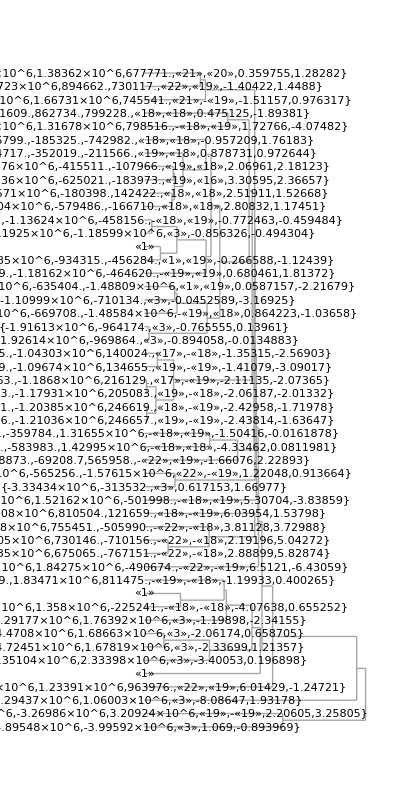

```mathematica
Dendrogram[chosenPCs,Right]
```

```mathematica
Length[FindClusters[chosenPCs]]
```

5

```mathematica
clusters=FindClusters[chosenPCs,10]
```

{{{2.05624×10^6,1.38362×10^6,677771.,1.92128×10^6,0.0571068,0.359755,1.28282},{1.00203×10^6,1.23391×10^6,963976.,1.74467×10^6,3.57652,6.01429,-1.24721},{1.18723×10^6,894662.,730117.,2.35936×10^6,3.52392,-1.40422,1.4488},{1.16937×10^6,1.66731×10^6,745541.,1.29044×10^6,-1.75955,-1.51157,0.976317}},{{-251439.,1.83471×10^6,811475.,-381605.,-4.00987,-1.19933,0.400265},{-1.29177×10^6,1.76392×10^6,1.11947×10^6,-1.00922×10^6,-5.68127,-1.19898,-2.34155},{-4.35104×10^6,2.33398×10^6,2.00254×10^6,-910699.,-8.26884,-3.40053,0.196898},{-4.4708×10^6,1.68663×10^6,1.51182×10^6,-202668.,-9.41814,-2.06174,0.658705},{-4.72451×10^6,1.67819×10^6,1.50539×10^6,-17488.3,-9.44357,-2.33699,1.21357}},{{1.48117×10^6,1.50765×10^6,228763.,-328936.,-4.8617,-4.35663,-0.26013},{3.99912×10^6,859098.,-1.05023×10^6,119716.,-2.76109,0.0882671,-1.14511},{931609.,862734.,799228.,556258.,7.97394,0.475125,-1.89381},{2.16128×10^6,1.358×10^6,-225241.,-480380.,-4.9581,-4.07638,0.655252}},{{1.52108×10^6,810504.,121659.,192701.,-0.897691,6.03954,1.53798},{1.2838×10^6,755451.,-505990.,-1.007×10^6,-5.13618,3.81128,3.72988},{1.07805×10^6,730146.,-710156.,-1.69371×10^6,-6.86686,2.19196,5.04272},{1.08335×10^6,675065.,-767151.,-1.70066×10^6,-7.89818,2.88899,5.82874}},{{488336.,-359784.,1.31655×10^6,-448138.,25.6003,-1.50416,-0.0161878},{563013.,-583983.,1.42995×10^6,-680288.,31.4587,-4.33462,0.0811981},{778873.,-69208.7,565958.,-1.11811×10^6,16.156,-1.66076,2.22893},{-944677.,-1.13624×10^6,-458156.,-196649.,15.1851,-0.772463,-0.459484},{-1.11925×10^6,-1.18599×10^6,-423666.,-173904.,16.1325,-0.856326,-0.494304}},{{836799.,-185325.,-742982.,498344.,5.13257,-0.957209,1.76183},{-864717.,-352019.,-211566.,447682.,6.40837,0.878731,0.972644},{-1.23676×10^6,-415511.,-107966.,494432.,5.00751,2.06961,2.18123},{-1.90571×10^6,-180398.,142422.,262648.,4.01181,2.51911,1.52668},{-1.59736×10^6,-625021.,-183973.,349048.,5.51854,3.30595,2.36657},{-1.7304×10^6,-579486.,-166710.,388631.,6.0195,2.80832,1.17451},{-938089.,-1.18162×10^6,-464620.,-165118.,12.5999,0.680461,1.81372},{-1.52049×10^6,-973897.,-452368.,-50915.3,11.9315,-0.219128,-1.23347},{-2.11735×10^6,-934315.,-456284.,-82508.1,10.5182,-0.266588,-1.12439},{-1.19925×10^6,-669708.,-1.48584×10^6,-220586.,0.482198,0.864223,-1.03658},{-1.23146×10^6,-635404.,-1.48809×10^6,-197176.,1.86231,0.0587157,-2.21679},{-3.33434×10^6,-313532.,-1.24533×10^6,1.21578×10^6,-11.796,0.617153,1.66977},{-1.91613×10^6,-964174.,-2.14117×10^6,-276127.,-5.32528,-0.765555,0.13961},{-1.92614×10^6,-969864.,-2.14059×10^6,-269220.,-5.08377,-0.894058,-0.0134883},{-3.2586×10^6,-565256.,-1.57615×10^6,1.04113×10^6,-11.0399,1.22048,0.913664}},{{266495.,-1.04303×10^6,140024.,309943.,-9.87157,-1.35315,-2.56903},{-441463.,-1.1868×10^6,216129.,92319.1,-10.1602,-2.11135,-2.07365},{415699.,-1.09674×10^6,134655.,318400.,-10.0523,-1.41079,-3.09017},{-444113.,-1.17931×10^6,205083.,100918.,-10.2957,-2.06187,-2.01332},{-614361.,-1.20385×10^6,246619.,41621.6,-10.1265,-2.42958,-1.71978},{-627796.,-1.21036×10^6,246657.,31567.4,-10.2685,-2.43814,-1.63647},{-1.10999×10^6,-710134.,-1.57649×10^6,-275951.,-1.68346,-0.0452589,-3.16925}},{{1.37324×10^6,1.31678×10^6,798516.,-294122.,10.1884,1.72766,-4.07482},{3.07388×10^6,1.52162×10^6,-501998.,-77046.4,0.870489,5.30704,-3.83859},{1.82127×10^6,1.84275×10^6,-490674.,-1.37647×10^6,-2.63217,6.5121,-6.43059}},{{3.40621×10^6,-3.26986×10^6,3.20924×10^6,237527.,-10.7879,2.20605,3.25805},{4.89548×10^6,-3.99592×10^6,2.56084×10^6,-830725.,-17.3778,1.069,-0.893969}},{{8.29437×10^6,1.06003×10^6,-2.857×10^6,450995.,-1.75346,-8.08647,1.93178}}}

```mathematica
Length[clusters]
Map[Length,clusters]
```

10

{4,5,4,4,5,15,7,3,2,1}

```mathematica
f[x_]:=x[[1]]
```

```mathematica
representVec=Map[f,clusters]
```

{{2.05624×10^6,1.38362×10^6,677771.,1.92128×10^6,0.0571068,0.359755,1.28282},{-251439.,1.83471×10^6,811475.,-381605.,-4.00987,-1.19933,0.400265},{1.48117×10^6,1.50765×10^6,228763.,-328936.,-4.8617,-4.35663,-0.26013},{1.52108×10^6,810504.,121659.,192701.,-0.897691,6.03954,1.53798},{488336.,-359784.,1.31655×10^6,-448138.,25.6003,-1.50416,-0.0161878},{836799.,-185325.,-742982.,498344.,5.13257,-0.957209,1.76183},{266495.,-1.04303×10^6,140024.,309943.,-9.87157,-1.35315,-2.56903},{1.37324×10^6,1.31678×10^6,798516.,-294122.,10.1884,1.72766,-4.07482},{3.40621×10^6,-3.26986×10^6,3.20924×10^6,237527.,-10.7879,2.20605,3.25805},{8.29437×10^6,1.06003×10^6,-2.857×10^6,450995.,-1.75346,-8.08647,1.93178}}

```mathematica
g[part_]:=(Position[chosenPCs,part])[[1]][[1]]
lines=Map[g,representVec]
```

{1,2,3,11,12,20,21,44,45,50}

```mathematica
allTraces=Drop[Normal[noL1iData[All,1]],1]
```

{client_001,client_002,client_003,client_004,client_005,client_006,client_007,client_008,server_001,server_002,server_003,server_004,server_009,server_010,server_011,server_012,server_013,server_014,server_015,server_016,server_017,server_018,server_019,server_020,server_021,server_022,server_023,server_024,server_025,server_026,server_027,server_028,server_029,server_030,server_031,server_032,server_033,server_034,server_035,server_036,server_037,server_038,server_039,spec_gcc_001,spec_gcc_002,spec_gcc_003,spec_gobmk_001,spec_gobmk_002,spec_perlbench_001,spec_x264_001}

```mathematica
findTrace[x_]:=allTraces[[x]]
chosenTraces=Map[findTrace,lines]
```

{client_001,client_002,client_003,server_003,server_004,server_016,server_017,spec_gcc_001,spec_gcc_002,spec_x264_001}